```mathematica
<<Eidomatica`
SetDirectory[NotebookDirectory[]];
$HistoryLength=0;
```

Revisions: {Eidomatica Package: 347, libEidomatica: Unknown}

## Import data

### Directories

```mathematica
sample1="../results/sample-1/plots/";
sample2="./results/sample-2/plots/";
sample3="./results/sample-3/plots/";
directories={sample1,sample2,sample3}
```

{../results/sample-1/plots/,./results/sample-2/plots/,./results/sample-3/plots/}

### Cell Position Data

```mathematica
sample1=Import["../test-data/sample-1/data.mx"];
sample2=Import["../test-data/sample-2/data.mx"];
sample3=Import["../test-data/sample-3/data.mx"];
data={sample1,sample2,sample3};
```

### Tracks

```mathematica
sample1Tracks=Import["../test-data/sample-1/tracks.wdx"];
sample2Tracks=Import["../test-data/sample-2/tracks.wdx"];
sample3Tracks=Import["../test-data/sample-3/tracks.wdx"];
tracks={sample1Tracks,sample2Tracks,sample3Tracks};
```

### Densities

```mathematica
sample1Bonne=Import["../test-data/sample-1/densities250-bonne.mx"];
sample2Bonne=Import["../test-data/sample-2/densities250-bonne.mx"];
sample3Bonne=Import["../test-data/sample-3/densities250-bonne.mx"];
bonne={sample1Bonne,sample2Bonne,sample3Bonn2};
```

```mathematica
sample1Densities=Import["../test-data/sample-1/densities250.mx"];
sample2Densities=Import["../test-data/sample-2/densities250.mx"];
sample3Densities=Import["../test-data/sample-3/densities250.mx"];
densities={sample1Densities,sample2Densities,sample3Densities};
```

### Colors

```mathematica
colors=ColorData[109,#]&/@{14,13,15}
```

{RGBColor[0, 0.7226017980018511, 0.9321946059944466],RGBColor[1., 0.06811595600706821, 0.0851449450088353],RGBColor[1., 0.7154761789941944, 0]}

## Cell counts

### Absolute cell counts

```mathematica
data//Dimensions
```

{3,3,420,3}

```mathematica
data[[All,All,All,1]]//Dimensions
```

{3,3,420}

```mathematica
counts=Map[Length,data[[All,All,All,1]],{3}];
```

```mathematica
{counts,Total/@counts}//Dimensions
```

{2,3}

### Relative cell counts

```mathematica
totals=Total/@counts;
relatives=Table[#/totals[[i]]&/@counts[[i]],{i,1,Length@counts}];
```

```mathematica
Dimensions@relatives
```

{3,3,420}

```mathematica
SetOptions[ConfidencePlot,BaseStyle->{8,FontFamily->"Helvetica"}];
ticks=Table[If[EvenQ[i],{i,i,{.01,0}},{i,"",{.005,0}}],{i,5,12}]
```

{{5,,{0.005,0}},{6,6,{0.01,0}},{7,,{0.005,0}},{8,8,{0.01,0}},{9,,{0.005,0}},{10,10,{0.01,0}},{11,,{0.005,0}},{12,12,{0.01,0}}}

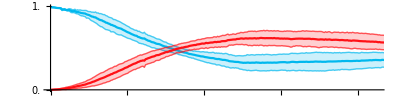

```mathematica
first=Show[MapThread[ConfidencePlot[Transpose@#1,Color->#2,PlotRange->{{4.,12.5},All},DataRange->{4,18},AxesOrigin->{4.,0}]&,Most/@{Transpose[relatives],colors}],AspectRatio->1/4,Ticks->{Automatic,{0.,.5,1.}}]
```

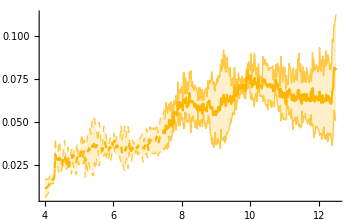

```mathematica
last=Show[{
ConfidencePlot[Transpose@(Take[#,105]&/@#[[1]]),Color->#[[2]],LineStyle->Dashed,DataRange->{4.,7.5},AxesOrigin->{4.,0}],
ConfidencePlot[Transpose@(Drop[#,105]&/@#[[1]]),Color->#[[2]],DataRange->{7.5,12.5},AxesOrigin->{4.,0}]},PlotRange->All
]&@(Last/@{Transpose[relatives],colors})
```

```mathematica
gr=Show[first,last];
```

```mathematica
Export["../tresults/relative_cell_counts+1,96*standard_error.pdf",gr]
```

```mathematica
ListLinePlot[Mean/@Transpose@relatives,PlotStyle->colors,PlotRange->{{4.,12.5},All},DataRange->{4,18},AxesOrigin->{4.,0}]
```

```mathematica
MapThread[ListLinePlot[Transpose@#1,PlotStyle->#2,PlotRange->{{4.,12.5},All},DataRange->{4,18},AxesOrigin->{4.,0}]&,{Transpose[relatives],colors}]
```

```mathematica
Export["../results/relative-cell_counts.pdf",Show[MapThread[ConfidencePlot[Transpose@#1,Color->#2,PlotRange->{All,All}]&,{Transpose[relatives],colors}]]]
```

## Radii

```mathematica
radii=Map[Norm@Last@#&,data[[All,All,All,1]],{4}];
```

```mathematica
sample1Mean=Map[Mean,radii[[1]],{2}];
```

```mathematica
radii//Dimensions
```

{3,3,420}

```mathematica
MapThread[StandardDeviationPlot[#1/sample1Mean[[2]],Color->#2,DataRange->{4,18},PlotRange->{{4.,12.5},All}]&,{radii[[1]],colors}]
```

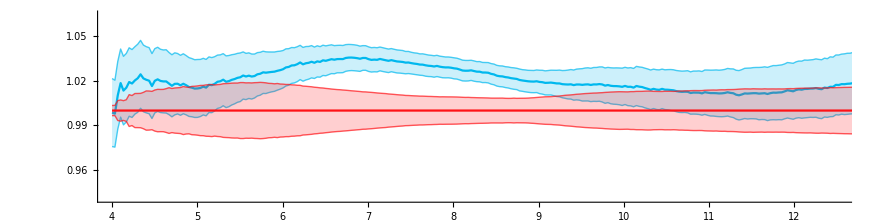

```mathematica
first=Show[MapThread[StandardDeviationPlot[#1/sample1Mean[[2]],Color->#2,DataRange->{4,18},PlotRange->{{4.,12.5},All},DeviationScaling->.3]&,Most/@{radii[[1]],colors}],AspectRatio->1/4]
```

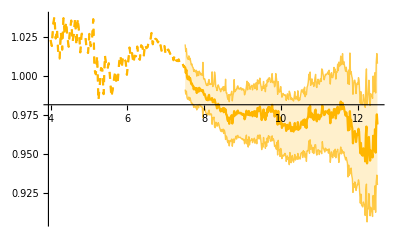

```mathematica
last=Show[{
StandardDeviationPlot[(Take[#[[1]]/sample1Mean[[2]],105]),Color->#[[2]],LineStyle->Dashed,DataRange->{4.,7.5},DeviationScaling->0],
StandardDeviationPlot[(Drop[#[[1]]/sample1Mean[[2]],105]),Color->#[[2]],DataRange->{7.5,12.5},DeviationScaling->.3]},PlotRange->All
]&@(Last/@{radii[[1]],colors})
```

```mathematica
Export["../results/radii+scaled-standard_deviation.pdf",Show[first,last]]
```

### Population radii

```mathematica
means=Map[Mean,radii,{3}];
```

```mathematica
means//Dimensions
```

{3,3,420}

```mathematica
normalization=Table[Mean@Flatten@means[[All,2,i]],{i,1,420}];
```

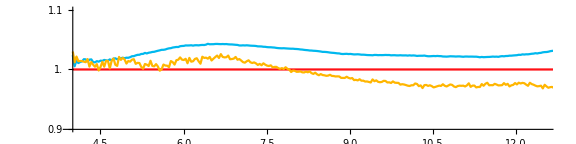

```mathematica
gr=Show[MapThread[ListLinePlot[Mean@#1/#3,PlotStyle->#2,ImageSize->Large,DataRange->{4,18},PlotRange->{{4.,12.5},{.9,1.1}}]&,{Transpose@means,colors,ConstantArray[normalization,3]}],AxesOrigin->{4.,.9},AspectRatio->1/4,Ticks->{Automatic,{.9,1.,1.1}}]
```

```mathematica
Export["../radii_long2.pdf",gr]
```

## cell tracks and straightness index

```mathematica
(*select tracklets from time interval*)
Clear[selectTrack,selectTracks];
selectTracks[tracks:{__Rule},start_Integer,end_Integer]:=DeleteCases[selectTrack[#,start,end]&/@tracks,{}]
selectTrack[track_Rule,start_Integer,end_Integer]:=If[First@track<start,If[Length@Last@track<(start-First@track+1),{},Take[Last@track,{start-First@track+1,UpTo[end-First@track+1]}]],Take[Last@track,UpTo[Max[0,end-First@track+1]]]]
```

```mathematica
<<ColorBrewer`
```

#### tracks

```mathematica
tracklets=DeleteCases[DeleteCases[selectTracks[#,50,90],x_/;Length@x<10],x_/;AnyTrue[Norm/@Differences@x,#>50&]]&/@sample1Tracks;
```

```mathematica
end=Map[Norm@First@Differences@#[[{1,-1}]]/(Total[Norm/@Differences@#])&,#]&/@tracklets;
```

```mathematica
Clear[testTrackVis]
testTrackVis[brewName_,n_:9,inverted_:False]:=Module[{brewfun,mesPlot,ectPlot},
brewfun=CreateColorFunction[brewName,n];
mesPlot=Graphics3D[MapThread[{brewfun[If[inverted,1-#1,#1]],Line[#2]}&,{mesoLUT,mesotracks}],Boxed->False];ectPlot=Graphics3D[MapThread[{brewfun[If[inverted,1-#1,#1]],Line[#2]}&,{ectoLUT,ectotracks}],Boxed->False];
GraphicsGrid[{{Show[mesPlot,ViewPoint->Front],Show[mesPlot,ViewPoint->Top]},{Show[ectPlot,ViewPoint->Front],Show[ectPlot,ViewPoint->Top]}}]
]
```

```mathematica
sphere=SphericalPlot3D[245,{theta,0,π},{phi,0,π},PlotStyle->None,Mesh->7,MeshStyle->Directive[AbsoluteThickness[1],Gray]]
```

```mathematica
brewfun=CreateColorFunction[Spectral,9];
```

```mathematica
mesPlotFront=Show[Graphics3D[MapThread[{AbsoluteThickness[2],brewfun[#1],Line[#2]}&,{end[[2]],tracklets[[2]]}],Boxed->False,ViewPoint->{0,-Infinity,0},ImageSize->300],sphere,PlotRange->{All,{0,300},All}]
```

-Graphics3D-

```mathematica
Export["../results/mesoPlotFront.pdf",mesPlotFront]
```

```mathematica
mesPlotTop=Show[Graphics3D[MapThread[{AbsoluteThickness[2],brewfun[#1],Line[#2]}&,{end[[2]],tracklets[[2]]}],Boxed->False,ViewPoint->{0,0,Infinity},ImageSize->300],sphere,PlotRange->{All,{0,300},All}]
```

```mathematica
ectPlotFront=Show[Graphics3D[MapThread[{AbsoluteThickness[2],brewfun[#1],Line[#2]}&,{end[[1]],tracklets[[1]]}],Boxed->False,ViewPoint->{0,-Infinity,0},ImageSize->300],sphere,PlotRange->{All,{0,300},All}]
```

-Graphics3D-

```mathematica
Export["../results/ectoPlotFront.pdf",ectPlotFront]
```

```mathematica
ectPlotTop=Show[Graphics3D[MapThread[{AbsoluteThickness[2],brewfun[#1],Line[#2]}&,{end[[1]],tracklets[[1]]}],Boxed->False,ViewPoint->{0,0,Infinity},ImageSize->300],sphere,PlotRange->{All,{0,300},All}]
```

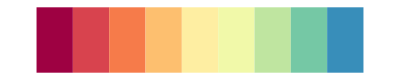

```mathematica
Graphics[Table[{CreateColorFunction[Spectral,11][(i-1)/9],Rectangle[{i-1,0},{i,1}]},{i,1,9}]]
```

```mathematica
rotationMatrix=RotationMatrix[Pi/2.4+.1,{1,0,0}].RotationMatrix[-Pi/3.2-.1,{0,1,0}].RotationMatrix[-.2,{0,0,1}];
```

```mathematica
sample1Tracks=Map[#[[1]]->(#.rotationMatrix&/@#[[2]])&,sample1Tracks,{2}];
```

#### Correlation analysis

```mathematica
colors=ColorData[109,#]&/@{14,13,15}
```

{RGBColor[0, 0.7226017980018511, 0.9321946059944466],RGBColor[1., 0.06811595600706821, 0.0851449450088353],RGBColor[1., 0.7154761789941944, 0]}

```mathematica
spherical=Transpose/@Map[ToSpherical[Last@#]&,tracklets,{2}];
```

```mathematica
ecto=(ListPlot[Transpose[{#,end[[1]]}],PlotStyle->colors[[1]]]&/@spherical[[1]])
```

```mathematica
meso=(ListPlot[Transpose[{#,end[[2]]}],PlotStyle->colors[[2]]]&/@spherical[[2]])
```

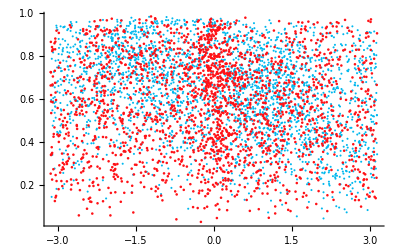
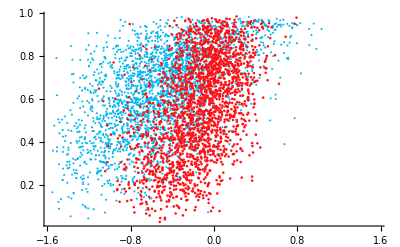
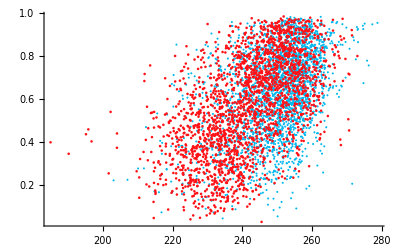

```mathematica
gr=MapThread[Show[#1,#2,PlotRange->#3,AxesOrigin->#4]&,{ecto,meso,{{{-Pi,Pi},Automatic},{{-Pi/2,Pi/2},Automatic},{Automatic,Automatic}},{{-Pi,0},{-Pi/2,0},Automatic}}]
```

```mathematica
MapThread[Export["../results/"<>#1<>"-correlation.pdf",#2]&,{{"latitude","longitude","radius"},gr}]
```

{../results/latitude-correlation.pdf,../results/longitude-correlation.pdf,../results/radius-correlation.pdf}

```mathematica
SpearmanRho[Sequence@@{#,end[[1]]}]&/@spherical[[1]]
```

{-0.270388,0.52594,0.406122}

```mathematica
SpearmanRho[Sequence@@{#,end[[2]]}]&/@spherical[[2]]
```

{-0.0456064,0.458189,0.577349}